```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 515 Kb

{Utilities`CleanSlate`,VariationalMethods`,System`,Global`}

```mathematica
Clear[q]
q = { x[t], y[t], θ[t], ϕ[t] } 
q[[1]]
q[[2]]
q[[3]]
q[[4]]
```

{x[t],y[t],θ[t],ϕ[t]}

x[t]

y[t]

θ[t]

ϕ[t]

```mathematica
D[q, t]
D[q[[1]], t]
D[q[[2]], t]
D[q[[3]], t]
D[q[[4]], t]
```

{x'[t],y'[t],θ'[t],ϕ'[t]}

x'[t]

y'[t]

θ'[t]

ϕ'[t]

```mathematica
Clear[r1]
r1 = { x[t], y[t] }
```

{x[t],y[t]}

```mathematica
D[r1, t]
```

{x'[t],y'[t]}

```mathematica
D[r1, t] . D[r1, t]
```

x'[t]^2+y'[t]^2

```mathematica
Clear[r2] 
r2 = { x[t] + b Cos[θ[t]] , y[t] + b Sin[θ[t]] }
```

{b Cos[θ[t]]+x[t],b Sin[θ[t]]+y[t]}

```mathematica
D[r2, t]
```

{x'[t]-b Sin[θ[t]] θ'[t],y'[t]+b Cos[θ[t]] θ'[t]}

```mathematica
D[r2, t] . D[r2, t]
```

(y'[t]+b Cos[θ[t]] θ'[t])^2+(x'[t]-b Sin[θ[t]] θ'[t])^2

```mathematica
D[r2, t] . D[r2, t] // Expand
```

x'[t]^2+y'[t]^2-2 b Sin[θ[t]] x'[t] θ'[t]+2 b Cos[θ[t]] y'[t] θ'[t]+b^2 Cos[θ[t]]^2 θ'[t]^2+b^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[r2, t] . D[r2, t] // Expand // Simplify
```

x'[t]^2+y'[t]^2-2 b Sin[θ[t]] x'[t] θ'[t]+2 b Cos[θ[t]] y'[t] θ'[t]+b^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 M ( D[r1, t] . D[r1, t]  ) + 1/2(1/2 M R^2 θ'[t]^2) +
1/2 m ( D[r2, t] . D[r2, t] // Expand // Simplify  ) + 1/2(1/2 m r^2 ϕ'[t]^2)
```

1/2 M (x'[t]^2+y'[t]^2)+1/4 M R^2 θ'[t]^2+1/2 m (x'[t]^2+y'[t]^2-2 b Sin[θ[t]] x'[t] θ'[t]+2 b Cos[θ[t]] y'[t] θ'[t]+b^2 θ'[t]^2)+1/4 m r^2 ϕ'[t]^2

```mathematica
Clear[V]
V = 0
```

0

```mathematica
Clear[ℒ]
ℒ = T - V
```

1/2 M (x'[t]^2+y'[t]^2)+1/4 M R^2 θ'[t]^2+1/2 m (x'[t]^2+y'[t]^2-2 b Sin[θ[t]] x'[t] θ'[t]+2 b Cos[θ[t]] y'[t] θ'[t]+b^2 θ'[t]^2)+1/4 m r^2 ϕ'[t]^2

```mathematica
D[D[ ℒ , D[q[[1]], t] ] ,t]- D[ ℒ, q[[1]] ] // Expand // Simplify 
D[D[ ℒ , D[q[[2]], t] ] ,t]- D[ ℒ, q[[2]] ]  // Expand  // Simplify 
D[D[ ℒ , D[q[[3]], t] ] ,t]- D[ ℒ, q[[3]] ] // Expand // Simplify 
D[D[ ℒ , D[q[[4]], t] ] ,t]- D[ ℒ, q[[4]] ]  // Expand // Simplify 

Table[
D[D[ ℒ , D[q[[i]], t] ] ,t]- D[ ℒ, q[[i]] ],
{i,1,4}] // Expand // Simplify  // TableForm
```

-b m Cos[θ[t]] θ'[t]^2+(m+M) x''[t]-b m Sin[θ[t]] θ''[t]

-b m Sin[θ[t]] θ'[t]^2+(m+M) y''[t]+b m Cos[θ[t]] θ''[t]

-b m Sin[θ[t]] x''[t]+b m Cos[θ[t]] y''[t]+1/2 (2 b^2 m+M R^2) θ''[t]

1/2 m r^2 ϕ''[t]

-b m Cos[θ[t]] θ'[t]^2+(m+M) x''[t]-b m Sin[θ[t]] θ''[t]
-b m Sin[θ[t]] θ'[t]^2+(m+M) y''[t]+b m Cos[θ[t]] θ''[t]
-b m Sin[θ[t]] x''[t]+b m Cos[θ[t]] y''[t]+1/2 (2 b^2 m+M R^2) θ''[t]
1/2 m r^2 ϕ''[t]

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

b m Cos[θ[t]] θ'[t]^2-(m+M) x''[t]+b m Sin[θ[t]] θ''[t]==0
b m Sin[θ[t]] θ'[t]^2-(m+M) y''[t]-b m Cos[θ[t]] θ''[t]==0
b m Sin[θ[t]] x''[t]-b m Cos[θ[t]] y''[t]-1/2 (2 b^2 m+M R^2) θ''[t]==0
-1/2 m r^2 ϕ''[t]==0

```mathematica
Clear[m,M,r,R,b]
M = 10 ;
m = 2 ;
R = 5 ;
r =1 ;
b = 2  ;
```

```mathematica
Clear[ics]
ics = { 
x[0] == 1,
x'[0] == -2 ,
y[0] == 3 ,
y'[0] == -4,
θ[0] == 5,
θ'[0] == -6 ,
ϕ[0] == 7 ,
ϕ'[0] == -8 
};
ics // TableForm
```

x[0]==1
x'[0]==-2
y[0]==3
y'[0]==-4
θ[0]==5
θ'[0]==-6
ϕ[0]==7
ϕ'[0]==-8

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[eqs,ics] , q , { t, 0, 10 } ]]
```

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t]}

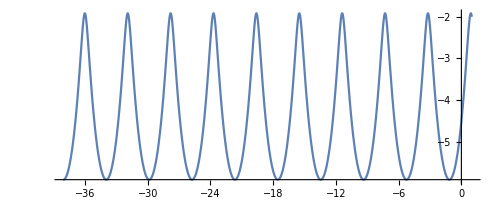
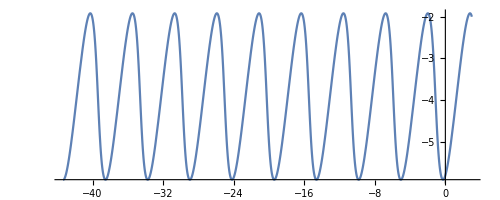
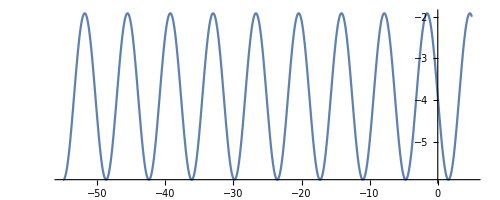
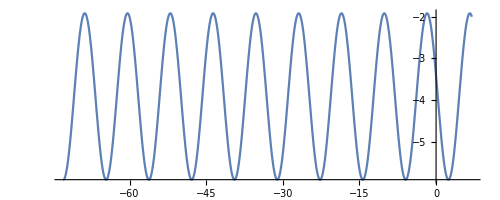

```mathematica
Table[
ParametricPlot[ { solution[t][[i,2]] , solution'[t][[1,2]] } , { t, 0, 10 } ]  , 
{ i , 1, 4 } ]
```